## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.25; Q=0.8;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.177836-7.20196×10^-7 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.125

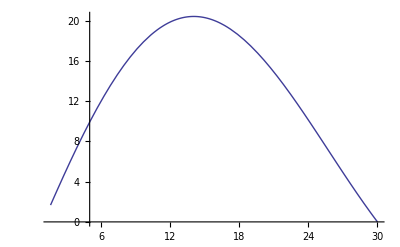

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-7.2021×10^-7},{30.2,-6.85795×10^-7},{30.4,-6.53245×10^-7},{30.6,-6.22338×10^-7},{30.8,-5.93102×10^-7},{31.,-5.65353×10^-7},{31.2,-5.39065×10^-7},{31.4,-5.14117×10^-7},{31.6,-4.90457×10^-7},{31.8,-4.67989×10^-7},{32.,-4.46654×10^-7},{32.2,-4.26379×10^-7},{32.4,-4.07144×10^-7},{32.6,-3.88853×10^-7},{32.8,-3.71458×10^-7},{33.,-3.54918×10^-7},{33.2,-3.39191×10^-7},{33.4,-3.24221×10^-7},{33.6,-3.09858×10^-7},{33.8,-2.96409×10^-7},{34.,-2.83497×10^-7},{34.2,-2.71177×10^-7},{34.4,-2.59479×10^-7},{34.6,-2.48292×10^-7},{34.8,-2.37673×10^-7},{35.,-2.2752×10^-7},{35.2,-2.17836×10^-7},{35.4,-2.08599×10^-7},{35.6,-1.99758×10^-7},{35.8,-1.91351×10^-7},{36.,-1.83355×10^-7},{36.2,-1.75661×10^-7},{36.4,-1.6838×10^-7},{36.6,-1.61355×10^-7},{36.8,-1.547×10^-7},{37.,-1.48289×10^-7},{37.2,-1.4217×10^-7},{37.4,-1.36381×10^-7},{37.6,-1.30782×10^-7},{37.8,-1.2545×10^-7},{38.,-1.20343×10^-7},{38.2,-1.15462×10^-7},{38.4,-1.10791×10^-7},{38.6,-1.06321×10^-7},{38.8,-1.02032×10^-7},{39.,-9.7943×10^-8},{39.2,-9.40193×10^-8},{39.4,-9.02612×10^-8},{39.6,-8.66634×10^-8},{39.8,-8.32207×10^-8},{40.,-7.99101×10^-8},{40.2,-7.67391×10^-8},{40.4,-7.36944×10^-8},{40.6,-7.07915×10^-8},{40.8,-6.79932×10^-8},{41.,-6.53158×10^-8},{41.2,-6.27487×10^-8},{41.4,-6.02932×10^-8},{41.6,-5.79221×10^-8},{41.8,-5.56652×10^-8},{42.,-5.34879×10^-8},{42.2,-5.13908×10^-8},{42.4,-4.93944×10^-8},{42.6,-4.74627×10^-8},{42.8,-4.56264×10^-8},{43.,-4.3847×10^-8},{43.2,-4.21487×10^-8},{43.4,-4.04996×10^-8},{43.6,-3.89268×10^-8},{43.8,-3.74514×10^-8},{44.,-3.59632×10^-8},{44.2,-3.45703×10^-8},{44.4,-3.32297×10^-8},{44.6,-3.19404×10^-8},{44.8,-3.07019×10^-8},{45.,-2.95121×10^-8},{45.2,-2.83708×10^-8},{45.4,-2.72652×10^-8},{45.6,-2.62085×10^-8},{45.8,-2.51886×10^-8},{46.,-2.42096×10^-8},{46.2,-2.32681×10^-8},{46.4,-2.2361×10^-8},{46.6,-2.14896×10^-8},{46.8,-2.06531×10^-8},{47.,-1.98431×10^-8},{47.2,-1.90665×10^-8},{47.4,-1.83191×10^-8},{47.6,-1.75999×10^-8},{47.8,-1.69034×10^-8},{48.,-1.624×10^-8},{48.2,-1.55985×10^-8},{48.4,-1.4981×10^-8},{48.6,-1.43841×10^-8},{48.8,-1.38113×10^-8},{49.,-1.32617×10^-8},{49.2,-1.27288×10^-8},{49.4,-1.22193×10^-8},{49.6,-1.17293×10^-8},{49.8,-1.12509×10^-8},{50.,-1.07963×10^-8},{50.2,-1.03556×10^-8},{50.4,-9.93166×10^-9},{50.6,-9.52201×10^-9},{50.8,-9.12992×10^-9},{51.,-8.75137×10^-9},{51.2,-8.38501×10^-9},{51.4,-8.03427×10^-9},{51.6,-7.69546×10^-9},{51.8,-7.36896×10^-9},{52.,-7.0531×10^-9},{52.2,-6.75049×10^-9},{52.4,-6.45857×10^-9},{52.6,-6.17791×10^-9},{52.8,-5.90598×10^-9},{53.,-5.64585×10^-9},{53.2,-5.39305×10^-9},{53.4,-5.1506×10^-9},{53.6,-4.91682×10^-9},{53.8,-4.69217×10^-9},{54.,-4.47511×10^-9},{54.2,-4.2654×10^-9},{54.4,-4.06441×10^-9},{54.6,-3.86995×10^-9},{54.8,-3.68275×10^-9},{55.,-3.50231×10^-9},{55.2,-3.32939×10^-9},{55.4,-3.16138×10^-9},{55.6,-2.99967×10^-9},{55.8,-2.84451×10^-9},{56.,-2.69477×10^-9},{56.2,-2.55056×10^-9},{56.4,-2.41151×10^-9},{56.6,-2.27782×10^-9},{56.8,-2.14884×10^-9},{57.,-2.02463×10^-9},{57.2,-1.90499×10^-9},{57.4,-1.78977×10^-9},{57.6,-1.6788×10^-9},{57.8,-1.57187×10^-9},{58.,-1.46885×10^-9},{58.2,-1.36995×10^-9},{58.4,-1.27439×10^-9},{58.6,-1.18244×10^-9},{58.8,-1.09419×10^-9},{59.,-1.00905×10^-9},{59.2,-9.27308×10^-10},{59.4,-8.48416×10^-10},{59.6,-7.72567×10^-10},{59.8,-6.99601×10^-10},{60.,-6.28899×10^-10}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

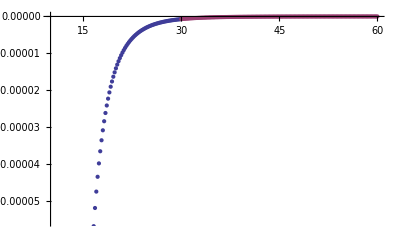

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

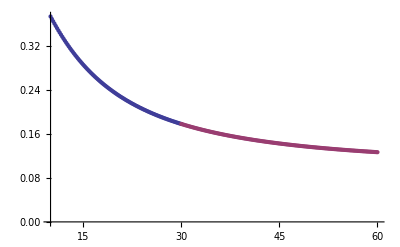

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.25/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.25/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.25/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.80/q=0.25/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```